# 概率

## 古典概型

## 抛硬币 1

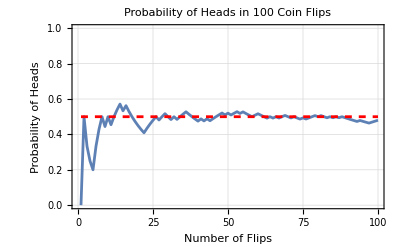

```mathematica
(*模拟抛硬币100次*)
coinFlips=RandomChoice[{0,1},100];

(*计算每次抛硬币后的正面累计次数*)
cumulativeHeads=Accumulate[coinFlips];

(*计算每次抛硬币后的正面概率*)
probabilityHeads=cumulativeHeads/Range@Length@coinFlips;

(*绘制正面概率的变化*)
ListLinePlot[{probabilityHeads,Table[0.5,{100}]},FrameLabel->{"Number of Flips","Probability of Heads"},PlotLabel->"Probability of Heads in 100 Coin Flips",GridLines->Automatic,PlotRange->{0,1},PlotStyle->{Automatic,{Red,Dashed}},PlotTheme->"Detailed"]
```

## 抛硬币 2

```mathematica
(*模拟10000次，每次抛10枚硬币*)
numTrials=10000;
numCoins=10;
(*记录每次试验的结果*)
results=Table[RandomChoice[{0,1},numCoins],{numTrials}];
(*计算每次试验中正面出现的次数*)
numHeads=Total/@results;
```

```mathematica
(*累计“正好出现6次正面”的次数*)
exactly6HeadsCounts=Module[{count=0},Table[If[numHeads[[i]]==6,count++];
count,{i,numTrials}]];

(*累计“至少出现6次正面”的次数*)
atLeast6HeadsCounts=Module[{count=0},Table[If[numHeads[[i]]>=6,count++];
count,{i,numTrials}]];
```

```mathematica
(*计算两个事件的当前概率*)
exactly6HeadsProbabilities=exactly6HeadsCounts/Range[numTrials];
atLeast6HeadsProbabilities=atLeast6HeadsCounts/Range[numTrials];
```

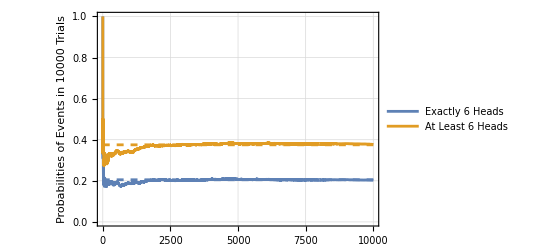

```mathematica
(*绘制两个事件的概率变化*)
Show[ListLinePlot[{exactly6HeadsProbabilities,atLeast6HeadsProbabilities},AxesLabel->{"Number of Trials","Probability"},FrameLabel->"Probabilities of Events in 10000 Trials",PlotLegends->Placed[{"Exactly 6 Heads","At Least 6 Heads"},{Right,Bottom}],PlotRange->All,GridLines->Automatic,PlotTheme->"Detailed"],Plot[{0.20508,0.3752},{x,0,10000},PlotStyle->Dashed]]
```

## 离散随机变量

## 离散数据

```mathematica
irisData=ExampleData[{"MachineLearning","FisherIris"},"Data"];
{sepalLength,sepalWidth,petalLength,petalWidth}=Table[irisData[[i,1,j]],{j,1,4},{i,1,150}];(*不考虑标签*)
axeslabels=ExampleData[{"Statistics","FisherIris"},"ColumnHeadings"]
```

{SepalLength,SepalWidth,PetalLength,PetalWidth,Species}

```mathematica
(*离散后的花萼数据*)
{discreteSepalLength,discreteSepalWidth}=Round[2#]/2&/@{sepalLength,sepalWidth};
discreteSepalData=Transpose@{discreteSepalLength,discreteSepalWidth};
```

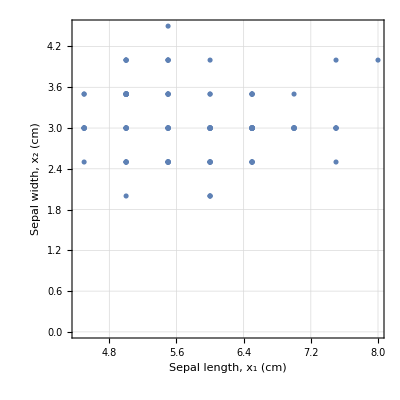

```mathematica
ListPlot[discreteSepalData,AspectRatio->1,GridLines->Automatic,PlotTheme->"Detailed",FrameLabel->{"Sepal length, x_1 (cm)","Sepal width, x_2 (cm)"}]
```

## 联合概率质量函数

```mathematica
Histogram3D[discreteSepalData]
```

-Graphics3D-

```mathematica
{g,{binCounts}}=Reap[Histogram3D[discreteSepalData,{{4.5,8,0.5},{2,5,0.5}},Function[{xbins,ybins,counts},Sow[counts]]]];
```

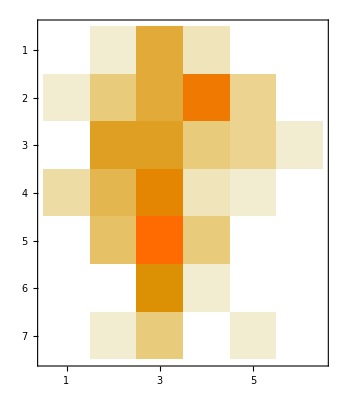

```mathematica
{g,MatrixPlot[First@binCounts]}//GraphicsRow
```

## 离散分布

## 均匀分布

正规数是指在某种进位下，其数位上的数字分布均匀、随机且无规律可循的无限小数

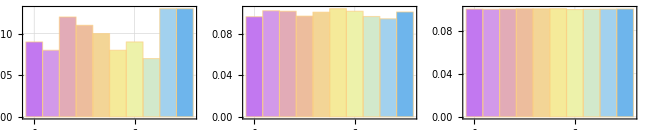

```mathematica
Histogram[RealDigits[N[Pi,#+1]-3][[1]](*圆周率小数点后的数字放在数组里*),{1},"PDF",PlotTheme->"Detailed",ChartStyle->"Pastel"]&/@{100,10000,1000000}(*小数点后位数*)//GraphicsRow
```

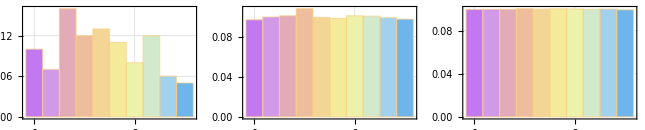

```mathematica
Histogram[RealDigits[N[E,#+1]-3][[1]],{1},"PDF",PlotTheme->"Detailed",ChartStyle->"Pastel"]&/@{100,10000,1000000}(*小数点后位数*)//GraphicsRow
```

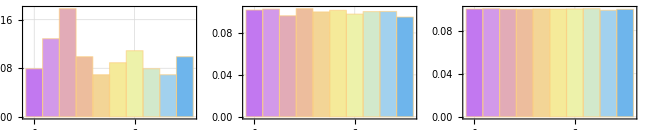

```mathematica
Histogram[RealDigits[N[Sqrt@2,#+1]-3][[1]],{1},"PDF",PlotTheme->"Detailed",ChartStyle->"Pastel"]&/@{100,10000,1000000}(*小数点后位数*)//GraphicsRow
```

## 二项分布

时，收敛于正态分布

```mathematica
{μ,σ}={Mean[BinomialDistribution[n,p]],StandardDeviation[BinomialDistribution[n,p]]}
```

{n p,√(n (1-p) p)}

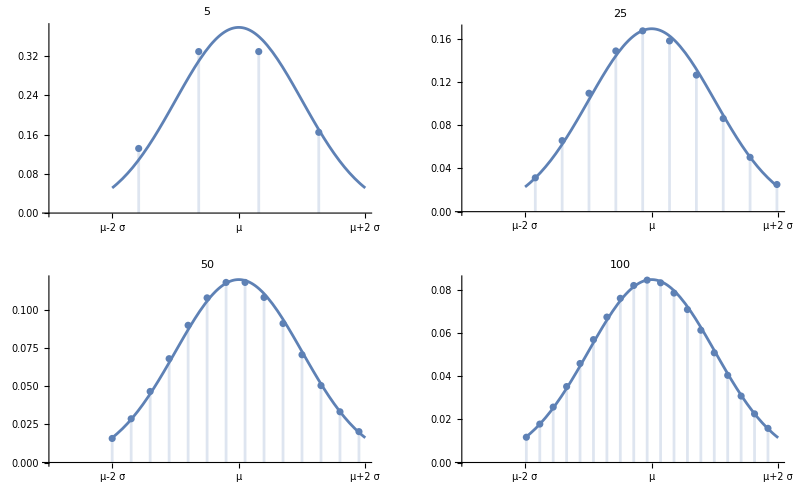

```mathematica
Block[{p=1/3},Table[Show[DiscretePlot[PDF[BinomialDistribution[n,p],k],{k,Ceiling[μ-2 σ],Floor[μ+2 σ]},PlotRange->{{μ-3 σ,μ+2 σ},All},AxesOrigin->{μ-3 σ,0}],Plot[PDF[NormalDistribution[μ,σ],x],{x,μ-2 σ,μ+2 σ}],Ticks->{{{μ-2 σ,HoldForm[μ-2 σ]},{μ,HoldForm[μ]},{μ+2 σ,HoldForm[μ+2 σ]}},Automatic},PlotRange->{{μ-3 σ,μ+2 σ},All},PlotLabel->n],{n,{5,25,50,100}}]]//ArrayReshape[#,{2,2}]&//GraphicsGrid
```

对比“抽样不放回”的超几何分布：总体越大，差别越小

```mathematica
Block[{p=.3,n=20},Table[DiscretePlot[{PDF[BinomialDistribution[n,p],k],PDF[HypergeometricDistribution[n,Round[nn p],nn],k]},{k,0,15},PlotRange->All,PlotLegends->{"Binomial","Hypergeometric"}],{nn,{100,200,400,800}}]]//ArrayReshape[#,{2,2}]&//GraphicsGrid
```

-Graphics-

## 泊松分布

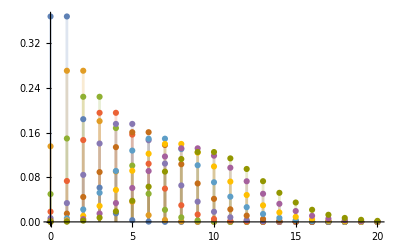

```mathematica
DiscretePlot[Table[PDF[PoissonDistribution[λ],k],{λ,Range@10}]//Evaluate,{k,0,20},PlotRange->All]
```

## 几何分布

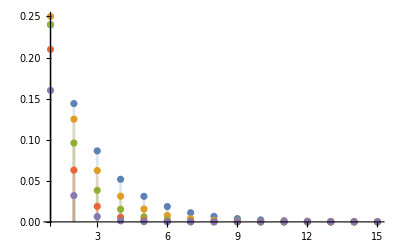

```mathematica
DiscretePlot[Table[PDF[GeometricDistribution[p],k],{p,{0.4,0.5,0.6,0.7,0.8}}]//Evaluate,{k,15},PlotRange->All]
```

## 连续随机变量

## 连续数据

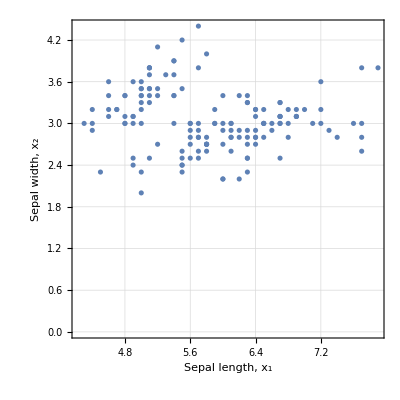

```mathematica
continuousSepalData=Transpose@{sepalLength,sepalWidth};
ListPlot[continuousSepalData,AspectRatio->1,GridLines->Automatic,PlotTheme->"Detailed",FrameLabel->{"Sepal length, x_1","Sepal width, x_2"}]
```

## 核密度估计

```mathematica
{SmoothHistogram3D[continuousSepalData,PlotTheme->"Detailed",AxesLabel->{"Sepal length, x_1","Sepal width, x_2"}],Show[SmoothDensityHistogram[continuousSepalData,Mesh->20],ListPlot[continuousSepalData,PlotStyle->{PointSize[Medium]}]]}//GraphicsRow
```

-Graphics-

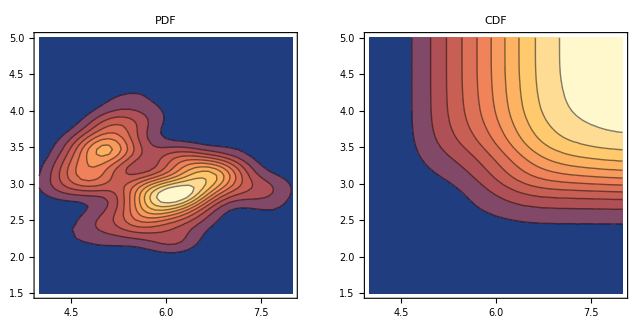

```mathematica
𝒟=SmoothKernelDistribution[continuousSepalData];
Table[ContourPlot[f[𝒟,{x,y}],{x,4,8},{y,1.5,5},PlotLabel->f,PlotRange->All,Contours->10,PlotRange->All],{f,{PDF,CDF}}]//GraphicsRow
```

## 连续分布

## 经验累积分布函数

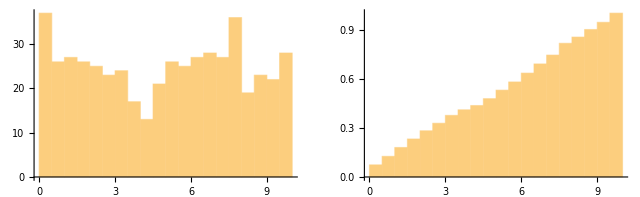

```mathematica
randomData=RandomReal[{0,10},500];
Histogram[randomData,{0.5},#]&/@{"Count","CDF"}//GraphicsRow
```

## 一元高斯分布

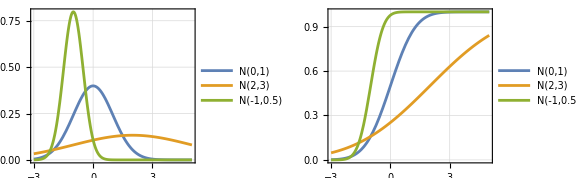

```mathematica
{Plot[{PDF[NormalDistribution[0,1],x],PDF[NormalDistribution[2,3],x],PDF[NormalDistribution[-1,.5],x]},{x,-3,5},PlotRange->All,PlotTheme->"Detailed",PlotLegends->Placed[{"N(0,1)","N(2,3)","N(-1,0.5)"},{Right,Top}]],Plot[{CDF[NormalDistribution[0,1],x],CDF[NormalDistribution[2,3],x],CDF[NormalDistribution[-1,.5],x]},{x,-3,5},PlotRange->All,PlotTheme->"Detailed",PlotLegends->Placed[{"N(0,1)","N(2,3)","N(-1,0.5)"},{Right,Bottom}]]}//GraphicsRow[#,ImageSize->Large]&
```

## 二元高斯分布

```mathematica
contourMultinormalDistribution[σ1_,σ2_,ρ_]:=ContourPlot[PDF[MultinormalDistribution[{0,0},{{σ1^2,ρ σ1 σ2},{ρ σ1 σ2,σ2^2}}],{x,y}],{x,-5,5},{y,-5,5},ColorFunction->"Rainbow",PlotRange->All]
```

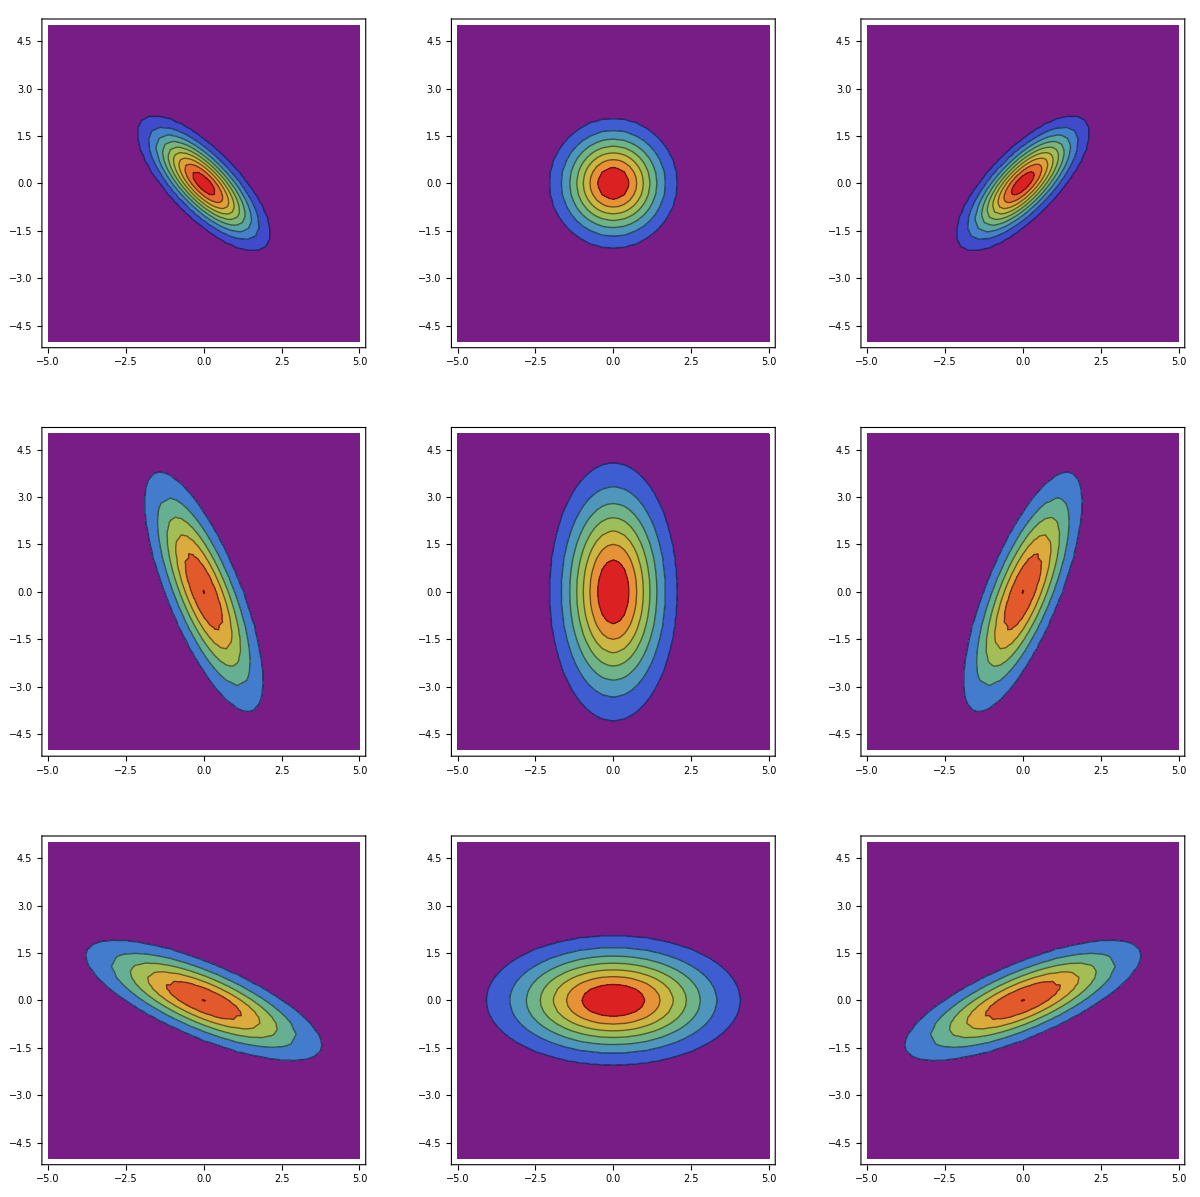

```mathematica
contourMultinormalDistribution@@#&/@{{1,1,-.75},{1,1,0},{1,1,.75},{1,2,-.75},{1,2,0},{1,2,.75},{2,1,-.75},{2,1,0},{2,1,.75}}//ArrayReshape[#,{3,3}]&//GraphicsGrid
```

## 拉普拉斯分布

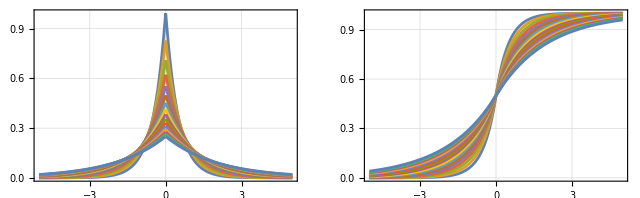

```mathematica
{Plot[Evaluate[PDF[LaplaceDistribution[0,#],x]&/@Table[i,{i,0.5,2.0,0.1}]],{x,-5,5},PlotRange->All,PlotTheme->"Detailed",PlotLegends->None],Plot[Evaluate[CDF[LaplaceDistribution[0,#],x]&/@Table[i,{i,0.5,2.0,0.1}]],{x,-5,5},PlotRange->All,PlotTheme->"Detailed",PlotLegends->None]}//GraphicsRow
```

```mathematica
Clear[μ,b];
Expectation[x,x\[Distributed]#]&@LaplaceDistribution[μ,b]//FullSimplify
Variance@LaplaceDistribution[μ,b]
```

μ

2 b^2

## 逻辑分布

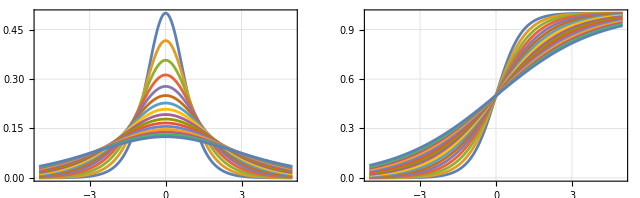

```mathematica
{Plot[Evaluate[PDF[LogisticDistribution[0,#],x]&/@Table[i,{i,0.5,2.0,0.1}]],{x,-5,5},PlotRange->All,PlotTheme->"Detailed",PlotLegends->None],Plot[Evaluate[CDF[LogisticDistribution[0,#],x]&/@Table[i,{i,0.5,2.0,0.1}]],{x,-5,5},PlotRange->All,PlotTheme->"Detailed",PlotLegends->None]}//GraphicsRow
```

对比高斯分布

```mathematica
Manipulate[{Plot[Evaluate[PDF[#,x]&/@{LogisticDistribution[0,i],NormalDistribution[0,1]}],{x,-5,5}],Plot[Evaluate[CDF[#,x]&/@{LogisticDistribution[0,i],NormalDistribution[0,1]}],{x,-5,5}]}//GraphicsRow,{i,0.5,2.0}]
```

## 学生 t-分布

自由度不断提高，接近于标准正态分布

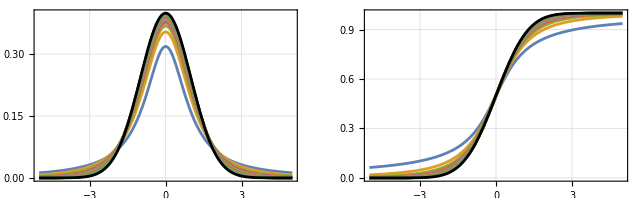

```mathematica
{Show[Plot[Evaluate[PDF[StudentTDistribution@#,x]&/@Range@30],{x,-5,5},PlotRange->All,PlotTheme->"Detailed",PlotLegends->None],Plot[PDF[NormalDistribution[],x],{x,-5,5},PlotStyle->Black]],Show[Plot[Evaluate[CDF[StudentTDistribution@#,x]&/@Range@30],{x,-5,5},PlotRange->All,PlotTheme->"Detailed",PlotLegends->None],Plot[CDF[NormalDistribution[],x],{x,-5,5},PlotStyle->Black]]}//GraphicsRow
```

## 对数正态分布

对数正态分布的随机变量取值只能为正值

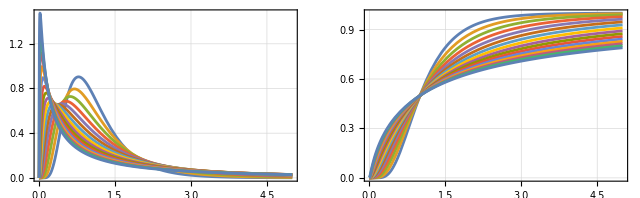

```mathematica
{Plot[Evaluate[PDF[LogNormalDistribution[0,#],x]&/@Table[i,{i,0.5,2.0,0.1}]],{x,0,5},PlotRange->All,PlotTheme->"Detailed",PlotLegends->None],Plot[Evaluate[CDF[LogNormalDistribution[0,#],x]&/@Table[i,{i,0.5,2.0,0.1}]],{x,0,5},PlotRange->All,PlotTheme->"Detailed",PlotLegends->None]}//GraphicsRow
```

## 指数分布

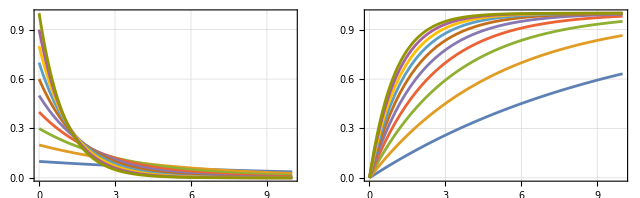

```mathematica
{Plot[Evaluate[PDF[ExponentialDistribution@#,x]&/@(Range@10/10)],{x,0,10},PlotRange->All,PlotTheme->"Detailed",PlotLegends->None],Plot[Evaluate[CDF[ExponentialDistribution@#,x]&/@(Range@10/10)],{x,0,10},PlotRange->All,PlotTheme->"Detailed",PlotLegends->None]}//GraphicsRow
```

## 卡方分布

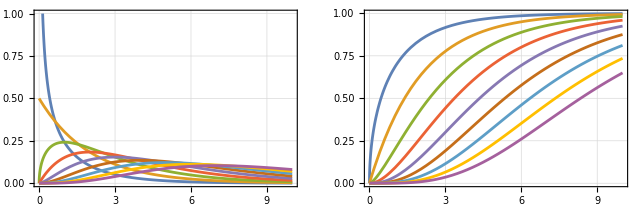

```mathematica
{Plot[Evaluate[PDF[ChiSquareDistribution@#,x]&/@Range@9],{x,0,10},PlotRange->{0,1},PlotTheme->"Detailed",PlotLegends->None],Plot[Evaluate[CDF[ChiSquareDistribution@#,x]&/@Range@9],{x,0,10},PlotRange->All,PlotTheme->"Detailed",PlotLegends->None]}//GraphicsRow
```

## F 分布

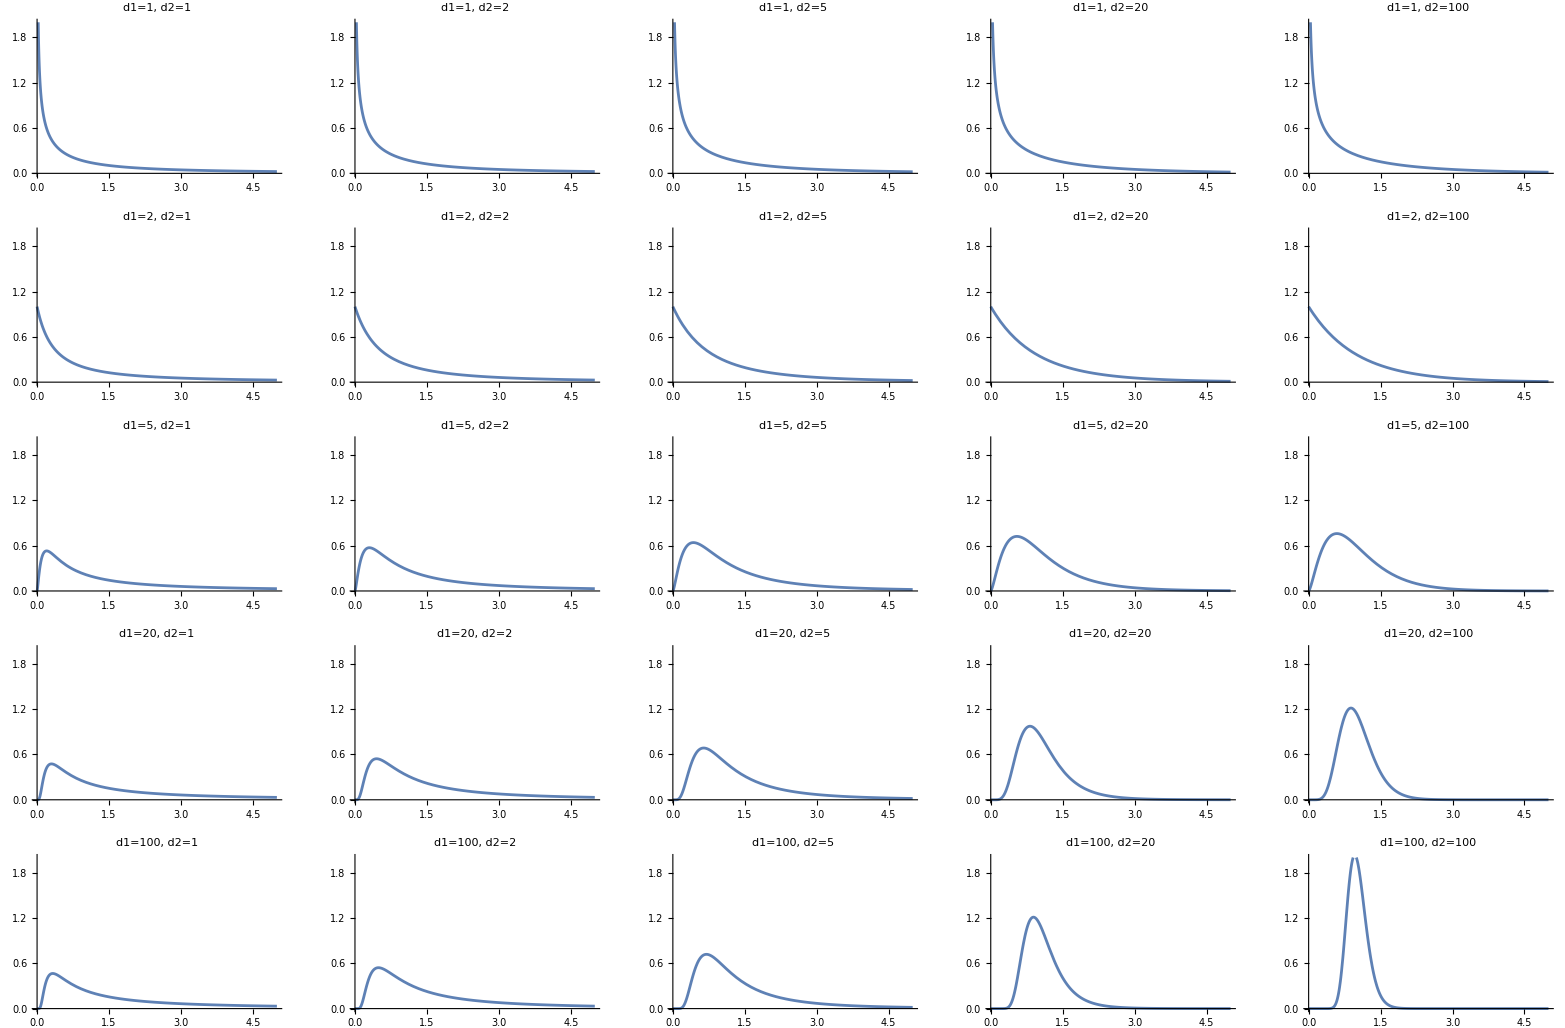

```mathematica
GraphicsGrid@Partition[Table[Plot[PDF[dist,x],{x,0,5},PlotTheme->"Minimal",PlotRange->{0,2},PlotLabel->StringForm["d1=``, d2=``",Sequence@@dist[[;;2]]]],{dist,FRatioDistribution@@@Flatten[Outer[{#1,#2}&,{1,2,5,20,100},{1,2,5,20,100}],1]}],5]
```

## Beta 分布

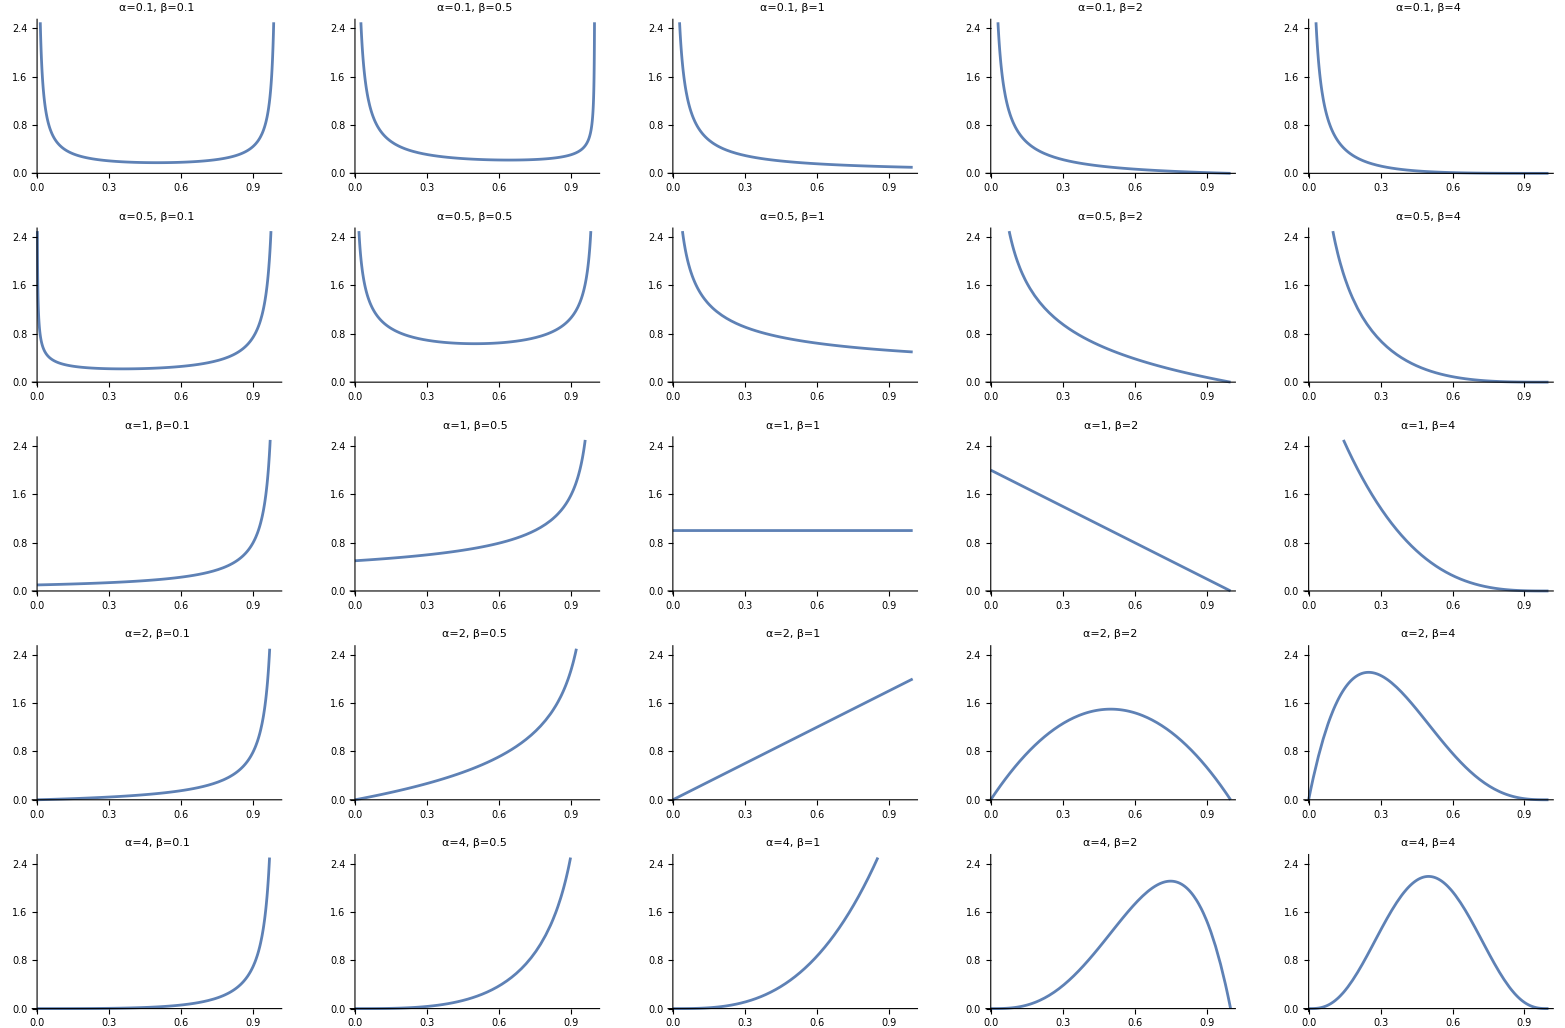

```mathematica
GraphicsGrid@Partition[Table[Plot[PDF[dist,x],{x,0,1},PlotTheme->"Minimal",PlotRange->{0,2.5},PlotLabel->StringForm["α=``, β=``",Sequence@@dist[[;;2]]]],{dist,BetaDistribution@@@Flatten[Outer[{#1,#2}&,{0.1,0.5,1,2,4},{0.1,0.5,1,2,4}],1]}],5]
```

```mathematica
Clear[α,β];
Expectation[x,x\[Distributed]#]&@BetaDistribution[α,β]
Variance@BetaDistribution[α,β]
```

α/(α+β)

(α β)/((α+β)^2 (1+α+β))

Beta 分布的众数，即概率密度函数曲线最大值所在位置

```mathematica
Maximize[{PDF[BetaDistribution[3,4],x],0<x<1},x]//Last
```

{x→2/5}

## Dirichlet 分布

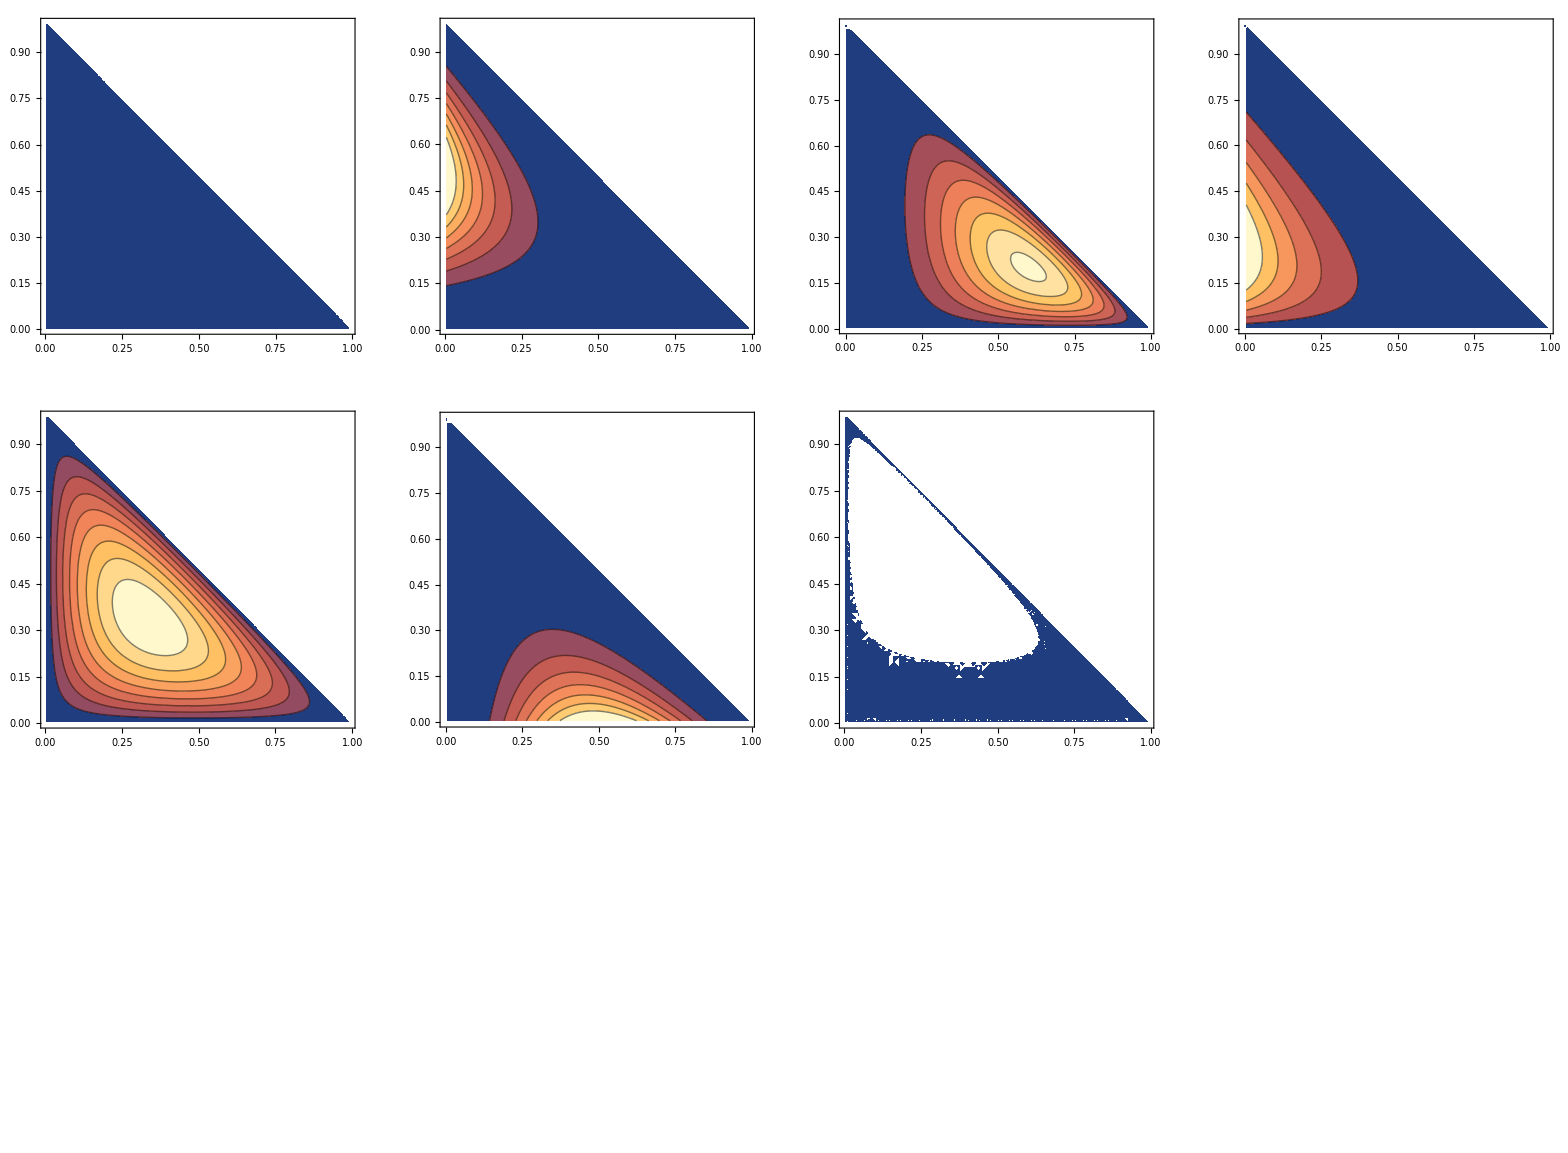

```mathematica
ContourPlot[PDF[DirichletDistribution@#,{x,y}],{x,0,1},{y,0,1},RegionFunction->Function[{x,y},x+y<1],PlotRange->All]&/@{{1,1,1},{1,4,4},{4,2,2},{1,2,4},{2,2,2},{4,1,4},{2,4,2},{2,1,4},{4,4,4},{4,4,1},{2,2,4},{4,2,1}}//ArrayReshape[#,{3,4}]&//GraphicsGrid
```